# Complex Functions

### Definitions

There are lots of ways to define functions f:ℂ->ℂ.

Taylor Series ∑_(k=0)^∞ (a_k(z-c))^k are useful when they converge i.e. |z-c|<R

Radius of convergence R=(lim_(k->∞) |(a_(k+1))/a_k|)^-1.

You can also use the root test lim_(k->∞) a_k^(1/k).

Analytic Continuation means connecting TS to extend definitions

All your favorite calculus functions extend to ℂ.

You can differentiate and integrate TS.

You can do algebra with TS.

f:ℂ→ℂ is differentiable if f(x+ⅈ y)=u(x,y)+ⅈ v(x,y) and satisfies the Cauchy Riemann (CR) equations

∂_x u | = |    ∂_y v
∂_y u | = | -∂_x v

If f is differentiable then ∂_xx u+∂_yy u | = | ∂_xx v+∂_yy v | =0.  Very useful for solving ∇^2 u=Δu=0. https://en.wikipedia.org/wiki/Potential_flow#Analysis_for_two-dimensional_flow

Differentiable functions f:ℂ→ℂ preserves right angles.   https://en.wikipedia.org/wiki/Conformal_map

```mathematica
f[z_]:= z^(1/4)
TabView[{
"in"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,0.2,3},{θ,0,2π},
Mesh->All],
"out"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,0.2,3},{θ,0,2π},
Mesh->All]
},2]
```

12

```mathematica
f[z_]:= z^(1/4)
TabView[{
"in"->ParametricPlot[ReIm[x+ⅈ y],{x,0.2,3},{y,0.5,4},
Mesh->All],
"out"->ParametricPlot[ReIm[f[x+ⅈ y]],{x,0.2,3},{y,0.5,4},
Mesh->All]
},2]
```

12

Such conformal maps are historically useful.  https://en.wikipedia.org/wiki/Joukowsky_transform
https://demonstrations.wolfram.com/JoukowskiAirfoilGeometry

Calculus functions extended to ℂ satisfy the same identities as the calculus functions

Most functions have zero and singularities.

Simple Poles look like 1/(z-z_0).  Double poles look like (z-z_0)^-2…

Zeros of order n  look like (z-z_0)^n.

The coefficient a_-1 sitting atop a pole (a_-1)/(z-z_0) is called a residue.  https://en.wikipedia.org/wiki/Residue_(complex_analysis)

The reason for calling it a_-1 is because it is (z-z_0)^-1 in the Laurent Series ∑_(k=-∞)^(+∞) (a_k(z-z_0))^k

Branch points are where multivalued parts of functions split.  Branch cuts are installed to choose a single branch.

Essential singularity means an isolated singularity that is not a pole.

Differentiable functions on ℂ have lots of names.

Holomorphic: differentiable on some open set in ℂ.

Analytic: Locally given by a convergent TS

Entire: Holomorphic on ℂ.

Lots of identities

Inherited from ℝ

Connecting functions you thought were separate.  For instance, why does tanh have the name it does?

Convergence: Complicated in ℝ.  Simple in ℂ.

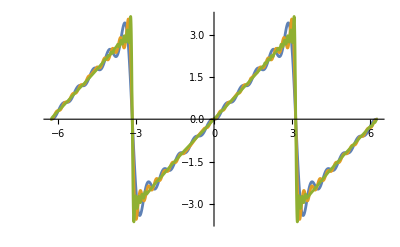

```mathematica
Clear[f,n,x]
f[n_][x_]:=2 Sum[(-1)^(k+1) Sin[k x]/k,{k, 1,n}]
Plot[{f[10][x],f[20][x],f[50][x]},{x,-2π, 2π}]
```

This effect motivates a need for “uniform convergence” in ℝ.  https://en.wikipedia.org/wiki/Uniform_convergence

Vitali’s Theorem: In ℂ, if the f_n are analytic and bounded on an open set D⊂ℂ and f_n[z]->f[z] then f[z] is analytic on D.

### Flashback to Log

Reminder:  ⅇ^(x + ⅈ y)=e^x e^(ⅈ y)=ⅇ^x(cos(y)+ⅈ sin(y)).  As a result 
	ⅇ^(z+ 2π ⅈ)=ⅇ^(x + y ⅈ + 2π ⅈ)=ⅇ^(x + (y+2π) ⅈ)=ⅇ^(x + y ⅈ)=ⅇ^z
The function ⅇ^z repeats every 2 π ⅈ in the complex direction.  It is completely defined by its behavior on the strip {z=x+ⅈ y∈ℂ: -π<y≤π}. This is the strip used to define the standard inverse function Log[z].  This standard logarithm satisfies
	Log[z]=Log[r ⅇ^(ⅈ θ)]=Log[r]+ i θ
because if z=r ⅇ^(ⅈ θ) then 
	 ⅇ^(Log[r] + ⅈ θ)=ⅇ^Log[r].ⅇ^(ⅈ θ)=r ⅇ^(ⅈ θ)=z.
Yes!  in this course, our book, Mathematica, Matlab, python, Julia and Wikipedia the inverse of ⅇ^z is written Log or log.   
“It is just how logs roll!”

```mathematica
f[z_]:=Log[z]
TabView[{
"3D"->ComplexPlot3D[f[z],{z,10},
PlotLegends->Automatic],
"ReIm"->Plot3D[{Re[f[x+ⅈ y]],Im[f[x+ⅈ y]]},
{x,-10,10},{y,-10,10},
PlotLegends->{"Re","Im"}],
"Sheets"->ParametricPlot3D[
{
{r Cos[θ], r Sin[θ],θ},
{r Cos[θ], r Sin[θ],Log[r]}
},
{r,0,10},{θ,-2π,4π},PlotPoints->100,
PlotLegends->{"Im","re"}]
}]
```

123

### Functions defined by Integrals

Functions of the form 
	f[z]=∫_a^b g(z,t) dt
are common where the integral is along the straight line connecting a and b in ℂ.  If g is analytic in z and continuous in t then f[z] is analytic.  This still works for a=-∞ and b=∞ as long as the integrals converge.

#### Example 1

f[z]=∫_0^∞ ⅇ^-t/(1+z t) dt
This makes sense as long as 1+z t≠0 for 0≤t<∞ since ⅇ^-t->0 fast as t->∞ along the real line.

```mathematica
Integrate[ E^(-t)/(1+ z t),{t,0, ∞}]
```

ConditionalExpression[(ⅇ^(1/z) Gamma[0,1/z])/z, Im[z]≠0||Re[z]≥0]

```mathematica
f[z_]:=(ⅇ^(1/z) Gamma[0,1/z])/z
ComplexPlot3D[f[z],{z,2 },PlotLegends->Automatic,Mesh->All]
```

-Graphics3D-

#### Example 2

Gamma Function Γ[z]=∫_0^∞ ⅇ^-t t^(z-1)dt

a) Since ⅇ^-t->0 very fast as t->∞ (along the real line) lim_(n->∞) ∫_1^n ⅇ^-t t^(z-1)dt exists.

b) If Re[z-1]<0 then there is a potential problem near t=0.  We need to make sure that  lim_(m->0^+) ∫_m^1 ⅇ^-t t^(z-1)dt make sense. Since |ⅇ^-t|≤1 for 0≤t<1  we have 
	∫_m^1 |ⅇ^-t t^(z-1)|dt≤∫_m^1|t^(z-1)|dt=∫_m^1 |t^(a-1 + b ⅈ)|dt=∫_m^1 |t^(a-1)||t^(b ⅈ)|dt=∫_m^1 |t^(a-1)|dt.
Remember that ∫_0^1 t^α dt=1/(1+α) if α>-1.  Mathematica knows the complex version

```mathematica
Integrate[t^α,{t,0,1}]
```

ConditionalExpression[1/(1+α), Re[α]>-1]

c) Putting these together shows that ∫_0^∞ ⅇ^-t t^(z-1)dt converges for Re[z]>0.  Mathematica knows this but apparently also knows how to plot the function for most values of z in the left half plane! Visually, there are poles at zero and the negative integers on the real axis.

```mathematica
Integrate[ E^(-t)t^(z-1),{t,0, ∞}]
f[z_]:=Gamma[z]
ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic,Mesh->All,PlotRange->{0,6}]
```

ConditionalExpression[Gamma[z], Re[z]>0]

-Graphics3D-

What is this mysterious Gamma function. 
https://en.wikipedia.org/wiki/Gamma_function

What is the two parameter version
https://en.wikipedia.org/wiki/Incomplete_gamma_function
with fancy functions you should ALWAYS read the documentation.

```mathematica
?Gamma
```

Remember integration by parts! 
	∫u dv=u v - ∫v du
or maybe
	∫f g'dt=f g - ∫g f' dt
or maybe the same thing with variables.  If we integrate by parts we get something interesting!
	(∫_m^n ⅇ^-t t^(z-1)dt=-ⅇ^-t t^(z-1)])_m^n+(z-1)∫_0^∞ ⅇ^-t t^(z-2)dt
Taking the limits as m->0^+ and n→∞ we get 
	Γ[z]=0+(z-1)Γ(z-1)
provided R[z]>0.  You can use this functional equation to define Γ on the new slice 	
	-1<Re[z]<0.  
This relationship explains the pole at z=1 and if you write this as
	Γ[z+1]=z Γ[z]
you can see that the Γ(z+1) generalizes the integer factorial 
	n! =(n-1) (n-1)!